# Cosmology, Problem 1: Evolution of Universe with general Energy of Particles

## Problem 4. Parametric plot: . Case

```mathematica
params = {α->1, β->1};
```

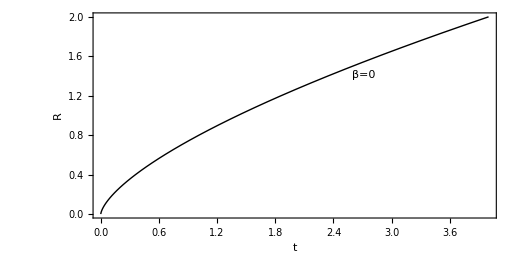

```mathematica
figPlotE0 = ParametricPlot[(α/2{η^3,η^2})/.params,{η,0,2}, PlotRange->{{0,4},{0,2}},
PlotStyle->{Black, Thick},
Frame->True, (*PlotLabel->"Evolution of R(t)(E=0)",*)
FrameLabel->{"t","R"},LabelStyle->(FontFamily->"Helvetica"),
PlotLabels->Placed[{"β=0"},Scaled[0.7]]]
```

```mathematica
Case
```

Case β<0

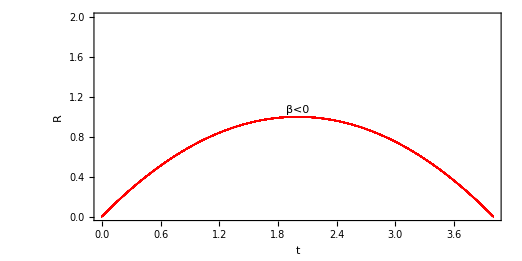

```mathematica
figPlotEN = ParametricPlot[(α/β{2+2/Sqrt[β] Sin[Sqrt[β]/2 η],Cos[Sqrt[β]/2 η]^2})/.params,{η,-100,100}, PlotRange->{{0,4},{0,2}},
PlotStyle->{Red, Thick},
Frame->True, (*PlotLabel->"Evolution of R(t)(E<0)",*)
FrameLabel->{"t","R"},LabelStyle->(FontFamily->"Helvetica"),
PlotLabels->Placed[{"β<0"},Above]]
```

```mathematica
Case
```

Case β>0

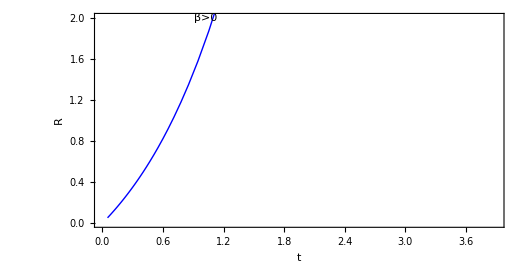

```mathematica
figPlotEP = ParametricPlot[({-Log[1- β Exp[α η]]/β,(α Exp[α η])/(1-β Exp[α η])})/.params,{η,-3,0}, PlotRange->{{0,3.9},{0,2}},
PlotStyle->{Blue, Thick},
Frame->True, (*PlotLabel->"Evolution of R(t)(E>0)"*)
FrameLabel->{"t","R"},LabelStyle->(FontFamily->"Helvetica"),
PlotLabels->Placed[{"β>0"},Above]]
```

Putting everything together

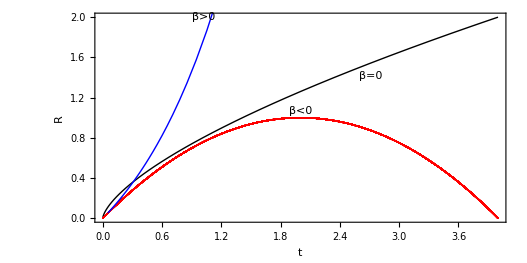

```mathematica
Show[figPlotE0,figPlotEN,figPlotEP]
```